{{{0.392569,0.0703502},{0.585079,0.0648637},{0.774568,0.0553937},{0.314556,0.0612526},{0.699572,0.04045},{0.470017,0.0682941}},{{0.392569,0.0410637},{0.585079,0.0382848},{0.774568,0.0313443},{0.314556,0.0325272},{0.699572,0.0202715},{0.470017,0.0403498}},{{0.392569,0.12149},{0.585079,0.11201},{0.774568,0.0553937},{0.314556,0.10578},{0.699572,0.06985},{0.470017,0.11794}}}

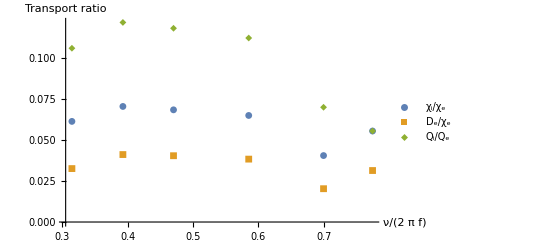

```mathematica
Plottot=Range[3];
{Plottot[[1]]}=Import["C:\\Users\\maxcu\\Google Drive\\0Research\\DIIID\\conference\\nu_scan\\ChiiChie.xlsx"];
{Plottot[[2]]}=Import["C:\\Users\\maxcu\\Google Drive\\0Research\\DIIID\\conference\\nu_scan\\DeChie.xlsx"];
{Plottot[[3]]}=Import["C:\\Users\\maxcu\\Google Drive\\0Research\\DIIID\\conference\\nu_scan\\QiQe.xlsx"];
Print[Plottot]

ListPlot(*ListPlot*)[
Plottot,

AxesLabel->{Style[ToExpression["\\frac{\\nu}{2 \\pi f}",TeXForm,HoldForm
]
,Bold,15],
Style["Transport ratio"
,Bold,15]},
(*PlotRange->{{0,10},{0,0.08}},*)
PlotMarkers->{Automatic,Small},
AxesStyle->Directive[Black,15],
PlotLegends->{ToExpression["\\frac{\\chi_i}{\\chi_e}",TeXForm
]
,
ToExpression["\\frac{D_e}{\\chi_e}",TeXForm
]
,
ToExpression["\\frac{Q_i}{Q_e}",TeXForm
]

}

(*PlotLegends->{"Chi_i/Chi_e
",
"D_e/Chi_e
",
"Q_i/Q_e
"
}*)
]
```

```mathematica
ToExpression["A\sqrt{a}",TeXForm]
```

√a A